```mathematica
Clear[t,a,p,aa,bb]
```

```mathematica
(* cf: A073058*)
```

```mathematica
(* F. M. Deking, "Recuurent Sets" ,Advances in Mathematics,vol. 44, no.1,April 1982, page 96, section 4.11*)
```

```mathematica
n0=4
```

4

```mathematica
(* substitution *)
```

```mathematica
s[1]={1,2,1,4,0,0,0,0,0,0}; s[2]={2,3,1,2,0,0,0,0,0}; s[3]={3,4,2,3,0,0,0,0,0};s[4]={1,4,3,4,0,0,0,0,0};
```

```mathematica
(* make matrix*)
```

```mathematica
M=Table[Table[Count[s[j],i],{i,1,n0}],{j,1,n0}]
```

{{2,1,0,1},{1,2,1,0},{0,1,2,1},{1,0,1,2}}

```mathematica
MatrixForm[M]
```

(2 | 1 | 0 | 1
1 | 2 | 1 | 0
0 | 1 | 2 | 1
1 | 0 | 1 | 2)

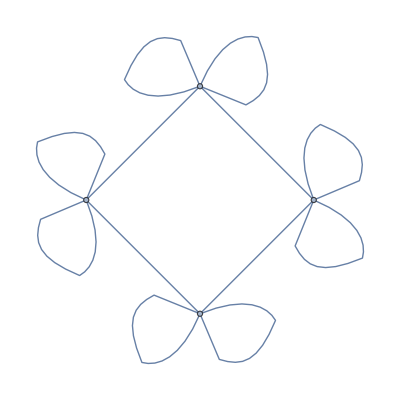

```mathematica
AdjacencyGraph[M]
```

```mathematica
(* make polynomial*)
```

```mathematica
Det[M-x*IdentityMatrix[n0]]
```

-16 x+20 x^2-8 x^3+x^4

```mathematica
(* solve Polynomial*)
```

```mathematica
NSolve[Det[M-x*IdentityMatrix[n0]]==0,x]
```

{{x→0.},{x→2.},{x→2.},{x→4.}}

```mathematica
Clear[s]
```

```mathematica
s[1]={1,2,1,4}; s[2]={2,3,1,2}; s[3]={3,4,2,3};s[4]={1,4,3,4};
```

```mathematica
t[a_] :=Flatten[s/@a];
```

```mathematica
w=Flatten[Table[s[i],{i,4}]]
```

{1,2,1,4,2,3,1,2,3,4,2,3,1,4,3,4}

```mathematica
p[0]=w;p[1]=t[p[0]];
```

```mathematica
p[n_]:=t[p[n-1]]
```

```mathematica
aa=p[8];
```

```mathematica
Length[aa]
```

262144

```mathematica
r=N[Table[{Cos[2*Pi*i/4],Sin[2*Pi*i/4]},{i,4}]]
```

{{0.,1.},{-1.,0.},{0.,-1.},{1.,0.}}

```mathematica
bb=aa /. 1->r[[1] ]/. 2->r[[2]]/. 3->r[[3]]/. 4->r[[4]];
```

```mathematica
cc=FoldList[Plus,{0,0},bb];
```

```mathematica
g0=ListPlot[cc,ColorFunction->Hue,PlotRange->All,Axes->False,ImageSize->2000,PlotStyle->PointSize[0.001]];
```

```mathematica
Export["Substitution_Tower_Level8.jpg",g0]
```

```mathematica
(*end*)
```